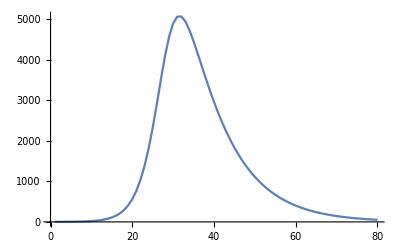

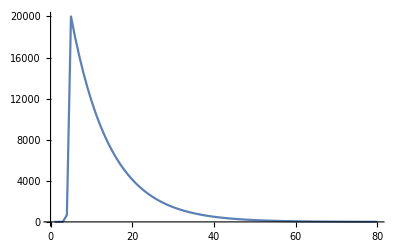

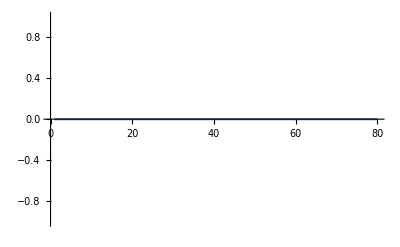

```mathematica
Clear["Global`*"];

EulerMethod[patientZeroPatch_, s0_,d_,beta_,alpha_, stepsCount_]:=(
patchesCount=Length[s0];
steps = Table[x, {x, 1,stepsCount}];

For[i=1,i<=patchesCount,i++,
sdata[i][1]=s0[[i]];
If[i==patientZeroPatch,idata[i][1]=1,idata[i][1]=0];

(*Print["sdata[",i,"][1] = ",sdata[i][1]];
Print["idata[",i,"][1] = ",idata[i][1]];*)
];

For[j=1,j<Length[steps],j++,
x=steps[[j]];
nextX = steps[[j+1]];
lambda=ConstantArray[0,patchesCount];

For[i = 1, i<=patchesCount,i++,
For[k = 1, k<=patchesCount,k++,
lambda[[i]]+=beta[[i]][[k]] idata[k][x];
];
];

For[i=1, i<=patchesCount,i++,
	currentN=n[[i]];
	sdata[i][nextX]=sdata[i][x]+d*currentN-d*sdata[i][x]-lambda[[i]]sdata[i][x];
	idata[i][nextX]=idata[i][x]+lambda[[i]]sdata[i][x]-d idata[i][x]-alpha idata[i][x];
	(*Print["sdata[",i,"][",nextX,"] = ",sdata[i][nextX]];
	Print["idata[",i,"][",nextX,"] = ",idata[i][nextX]];*)
	sdata[i][nextX]=Max[0, Min[n[[i]], sdata[i][nextX]]];
	idata[i][nextX]=Max[0, Min[n[[i]], idata[i][nextX]]];
];
];

results=ConstantArray[{},patchesCount];

For[i=1,i≤patchesCount,i++,
results[[i]]=Table[{j, idata[i][j]}, {j, 1, stepsCount}];
];

results
);

stepsCount=80;
alpha = 0.1;
patientZeroPatch=1;
d=0;
n={10000,20000,2000};
beta = {{0.00005,0,0},
	  {0.000005,0.004 ,0},
	  {0,0,0.01}};

(* Remove the 1 that is patient zero *)
s0=Map[Function[x,x-1],n];

results=EulerMethod[patientZeroPatch,s0,d,beta,alpha,stepsCount];

For[i=1,i≤Length[results],i++,
Print[ListPlot[results[[i]],PlotRange->All, Joined->True]];
]
```